```mathematica
FP =FullSimplify[Solve[r*x*(1-x/k)==x^2/(1+x^2),x]]
```

{{x→0},{x→1/6 (2 k+(2 2^(1/3) (3 r+k (3-k r)))/(9 k^2 r^2-18 k r^3-2 k^3 r^3+√(r^3 (k^2 r (9 k-2 (9+k^2) r)^2+4 (3 r+k (3-k r))^3)))^(1/3)-1/r 2^(2/3) (9 k^2 r^2-18 k r^3-2 k^3 r^3+√(r^3 (k^2 r (9 k-2 (9+k^2) r)^2+4 (3 r+k (3-k r))^3)))^(1/3))},{x→1/12 (4 k+(4 (-2)^(1/3) (-3 k+(-3+k^2) r))/(9 k^2 r^2-18 k r^3-2 k^3 r^3+√(r^3 (k^2 r (9 k-2 (9+k^2) r)^2+4 (3 r+k (3-k r))^3)))^(1/3)+1/r 2^(2/3) (1-ⅈ √3) (9 k^2 r^2-18 k r^3-2 k^3 r^3+√(r^3 (k^2 r (9 k-2 (9+k^2) r)^2+4 (3 r+k (3-k r))^3)))^(1/3))},{x→1/12 (4 k+1/r 2^(2/3) (1+ⅈ √3) (9 k^2 r^2-18 k r^3-2 k^3 r^3+√(r^3 (k^2 r (9 k-2 (9+k^2) r)^2+4 (3 r+k (3-k r))^3)))^(1/3)+((-3 k+(-3+k^2) r) Root2.52-4.36 ⅈRoot[128+#1^3&,2]2.5198420997897464)/(9 k^2 r^2-18 k r^3-2 k^3 r^3+√(r^3 (k^2 r (9 k-2 (9+k^2) r)^2+4 (3 r+k (3-k r))^3)))^(1/3))}}

```mathematica
Manipulate[
Plot[{r*(1-x/k),x/(1+x^2)},{x,0,20},PlotRange->{0,1}],
{{k,3},1,40},{{r,0.5},0,1}]
```

```mathematica
krofx=Solve[{r*(1-x/k)==x/(1+x^2),D[r*(1-x/k),x]==D[x/(1+x^2),x]},{k,r}]
```

{{k→(2 x^3)/(-1+x^2),r→(2 x^3)/((1+x^2)^2)}}

```mathematica
kcVSrc =Flatten[{k/.krofx,r/.krofx}]
```

{(2 x^3)/(-1+x^2),(2 x^3)/((1+x^2)^2)}

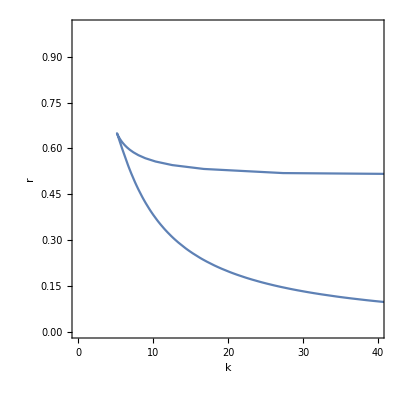

```mathematica
ParametricPlot[kcVSrc,{x,1.01,100},PlotRange->{{0,40},{0,1}},AspectRatio->1,Frame->True,FrameLabel->{"k","r"}]
```

```mathematica
Manipulate[
s=NDSolve[{x'[t]==r*x[t]*(1-(x[t]/k))-x[t]^2/(1+x[t]^2),x[0]==initial},x,{t,0,30}];
LogPlot[Evaluate[x[t]/.s],{t,0,30},PlotRange->{0.1,50},Frame->True,FrameLabel->{"Time","Population size x(t)"}],
{k,1,40},{r,0,1},{initial,0,50}]
```